```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.0001,1,0]],B:=Inverse[β[ω,0.0001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,8000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

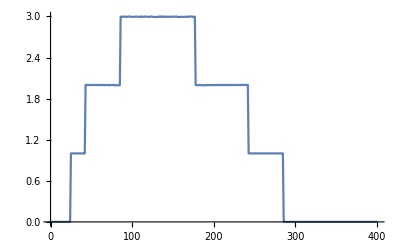

```mathematica
ListLinePlot[Table[tr[ω,0.0001,1,0],{ω,0,4,0.01}]]
```

```mathematica
RandomSample[Join[Flatten[Table[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],3]],Table[imp,58]]]
```

{imp8,imp,imp,imp,imp,imp,imp9,imp,imp5,imp,imp11,imp13,imp,imp,imp5,imp10,imp,imp,imp14,imp6,imp1,imp,imp2,imp,imp3,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp1,imp3,imp3,imp,imp14,imp5,imp12,imp1,imp9,imp,imp,imp10,imp,imp,imp,imp,imp4,imp9,imp,imp,imp13,imp,imp2,imp,imp7,imp,imp,imp,imp,imp,imp,imp7,imp6,imp11,imp13,imp,imp,imp,imp7,imp,imp,imp,imp12,imp,imp6,imp,imp,imp14,imp,imp8,imp8,imp2,imp,imp,imp,imp,imp4,imp12,imp4,imp10,imp,imp,imp,imp,imp11,imp}

```mathematica
m35[ω_,ϵ1_,ϵ2_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ2]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ2]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ2]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp8,imp,imp,imp,imp,imp,imp9,imp,imp5,imp,imp11,imp13,imp,imp,imp5,imp10,imp,imp,imp14,imp6,imp1,imp,imp2,imp,imp3,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp1,imp3,imp3,imp,imp14,imp5,imp12,imp1,imp9,imp,imp,imp10,imp,imp,imp,imp,imp4,imp9,imp,imp,imp13,imp,imp2,imp,imp7,imp,imp,imp,imp,imp,imp,imp7,imp6,imp11,imp13,imp,imp,imp,imp7,imp,imp,imp,imp12,imp,imp6,imp,imp,imp14,imp,imp8,imp8,imp2,imp,imp,imp,imp,imp4,imp12,imp4,imp10,imp,imp,imp,imp,imp11,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>3,3,tra1]]
```

```mathematica
Mean[Table[m35[0.5,0.3,0.9],1000]]
```

0.655468

```mathematica
Table[{ω,Mean[Table[m35[ω,0.3,0.9],2000]]},{ω,Range[0,1.5,0.01]}]
```

{{0.,0.0000193831},{0.01,0.0000117094},{0.02,0.0000177488},{0.03,0.0000269874},{0.04,0.0000451012},{0.05,0.0000713676},{0.06,0.0000978472},{0.07,0.000156961},{0.08,0.000198513},{0.09,0.000266668},{0.1,0.000342217},{0.11,0.00047354},{0.12,0.000564792},{0.13,0.000670424},{0.14,0.000840985},{0.15,0.00109635},{0.16,0.00139615},{0.17,0.00183758},{0.18,0.00240382},{0.19,0.00316635},{0.2,0.00483826},{0.21,0.00675472},{0.22,0.0108932},{0.23,0.0243112},{0.24,0.0896591},{0.25,0.157359},{0.26,0.231509},{0.27,0.293911},{0.28,0.361795},{0.29,0.406799},{0.3,0.431168},{0.31,0.460081},{0.32,0.487362},{0.33,0.504866},{0.34,0.525466},{0.35,0.539137},{0.36,0.538779},{0.37,0.552251},{0.38,0.552233},{0.39,0.555165},{0.4,0.531665},{0.41,0.526424},{0.42,0.81187},{0.43,1.19282},{0.44,0.897667},{0.45,0.72775},{0.46,0.659155},{0.47,0.617124},{0.48,0.625556},{0.49,0.636483},{0.5,0.659259},{0.51,0.697119},{0.52,0.712438},{0.53,0.739572},{0.54,0.751861},{0.55,0.776305},{0.56,0.807215},{0.57,0.839672},{0.58,0.886365},{0.59,0.846473},{0.6,0.902671},{0.61,0.929308},{0.62,0.955484},{0.63,0.939695},{0.64,0.982222},{0.65,0.967289},{0.66,1.01502},{0.67,1.01485},{0.68,1.01685},{0.69,1.05197},{0.7,1.0371},{0.71,1.07165},{0.72,1.07573},{0.73,1.09222},{0.74,1.12139},{0.75,1.10029},{0.76,1.10529},{0.77,1.10706},{0.78,1.15346},{0.79,1.16949},{0.8,1.17221},{0.81,1.1635},{0.82,1.16006},{0.83,1.14691},{0.84,1.10258},{0.85,1.00182},{0.86,1.12523},{0.87,0.950621},{0.88,0.823077},{0.89,0.791059},{0.9,0.845224},{0.91,0.857944},{0.92,0.948958},{0.93,1.00033},{0.94,1.05828},{0.95,1.14904},{0.96,1.20182},{0.97,1.26291},{0.98,1.35895},{0.99,1.36073},{1.,1.38217},{1.01,1.48046},{1.02,1.35103},{1.03,0.78043},{1.04,0.368664},{1.05,0.550805},{1.06,0.623499},{1.07,0.543462},{1.08,0.45541},{1.09,0.401163},{1.1,0.375084},{1.11,0.360217},{1.12,0.371866},{1.13,0.379316},{1.14,0.364417},{1.15,0.375199},{1.16,0.380847},{1.17,0.398161},{1.18,0.419078},{1.19,0.427437},{1.2,0.460573},{1.21,0.485655},{1.22,0.536731},{1.23,0.554243},{1.24,0.532514},{1.25,0.596968},{1.26,0.644985},{1.27,0.581007},{1.28,0.611515},{1.29,0.607151},{1.3,0.624832},{1.31,0.634127},{1.32,0.62353},{1.33,0.668716},{1.34,0.614357},{1.35,0.6724},{1.36,0.668376},{1.37,0.70073},{1.38,0.691958},{1.39,0.660628},{1.4,0.688049},{1.41,0.705851},{1.42,0.710818},{1.43,0.713125},{1.44,0.747752},{1.45,0.627738},{1.46,0.489824},{1.47,0.572949},{1.48,0.589082},{1.49,0.639971},{1.5,0.636595}}

```mathematica
Table[{ω,Mean[Table[m35[ω,0.9,0.3],2000]]},{ω,Range[0,1.5,0.01]}]
```

{{0.,0.0000341536},{0.01,0.0000215223},{0.02,0.0000307048},{0.03,0.0000379717},{0.04,0.0000601358},{0.05,0.0000894239},{0.06,0.000114204},{0.07,0.000179714},{0.08,0.000256393},{0.09,0.00033491},{0.1,0.000454711},{0.11,0.000544706},{0.12,0.000650531},{0.13,0.000846376},{0.14,0.00106886},{0.15,0.00130539},{0.16,0.00167868},{0.17,0.00217234},{0.18,0.00316175},{0.19,0.00408964},{0.2,0.00545564},{0.21,0.00816151},{0.22,0.0122921},{0.23,0.0279241},{0.24,0.0924978},{0.25,0.139277},{0.26,0.18629},{0.27,0.24289},{0.28,0.29256},{0.29,0.342153},{0.3,0.359865},{0.31,0.406569},{0.32,0.4238},{0.33,0.44164},{0.34,0.451498},{0.35,0.458039},{0.36,0.483592},{0.37,0.48659},{0.38,0.498507},{0.39,0.492026},{0.4,0.487364},{0.41,0.480796},{0.42,0.848559},{0.43,1.2451},{0.44,0.946501},{0.45,0.753626},{0.46,0.65919},{0.47,0.611175},{0.48,0.584755},{0.49,0.584046},{0.5,0.578746},{0.51,0.597283},{0.52,0.607013},{0.53,0.629174},{0.54,0.63681},{0.55,0.673547},{0.56,0.680691},{0.57,0.719342},{0.58,0.725955},{0.59,0.736944},{0.6,0.777189},{0.61,0.799565},{0.62,0.808065},{0.63,0.82658},{0.64,0.853923},{0.65,0.844885},{0.66,0.879725},{0.67,0.885201},{0.68,0.901558},{0.69,0.9164},{0.7,0.906395},{0.71,0.945306},{0.72,0.942607},{0.73,0.97064},{0.74,0.987125},{0.75,0.985301},{0.76,1.00295},{0.77,0.978469},{0.78,1.02473},{0.79,1.02898},{0.8,1.05154},{0.81,1.0415},{0.82,1.03012},{0.83,1.03208},{0.84,0.986457},{0.85,1.04831},{0.86,1.16352},{0.87,1.03492},{0.88,0.834729},{0.89,0.728776},{0.9,0.759583},{0.91,0.763731},{0.92,0.801342},{0.93,0.844187},{0.94,0.914445},{0.95,0.982025},{0.96,1.011},{0.97,1.0907},{0.98,1.13196},{0.99,1.18035},{1.,1.16717},{1.01,1.27142},{1.02,1.18024},{1.03,0.793958},{1.04,0.425352},{1.05,0.539873},{1.06,0.566941},{1.07,0.473054},{1.08,0.388462},{1.09,0.344844},{1.1,0.331854},{1.11,0.342378},{1.12,0.343945},{1.13,0.346272},{1.14,0.346507},{1.15,0.343329},{1.16,0.327678},{1.17,0.347383},{1.18,0.344863},{1.19,0.35998},{1.2,0.365519},{1.21,0.379946},{1.22,0.406207},{1.23,0.422776},{1.24,0.417419},{1.25,0.45448},{1.26,0.494114},{1.27,0.449342},{1.28,0.464125},{1.29,0.46113},{1.3,0.499449},{1.31,0.487888},{1.32,0.479076},{1.33,0.498995},{1.34,0.479636},{1.35,0.51164},{1.36,0.517561},{1.37,0.53895},{1.38,0.52814},{1.39,0.52611},{1.4,0.521355},{1.41,0.539707},{1.42,0.535791},{1.43,0.546832},{1.44,0.569442},{1.45,0.475421},{1.46,0.413177},{1.47,0.438978},{1.48,0.460838},{1.49,0.479526},{1.5,0.496804}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_20_nb_15t35.dat",%168]
Export["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_15_nb_20t35.dat",%169]
```

/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_20_nb_15t35.dat

/home/shardulmukim/PhD/fwi/7AGNR/two_imp/na_15_nb_20t35.dat